```mathematica
ClearAll["Global`*"];
```

### Wprowadzenie wartości dla przyspieszenia ziemskiego ( "g" ) , wysokości lustra wody nad otworem ( "h_o" ) i odległości otworu od dna basenu ( "h_1" ).

```mathematica
g=9.81;          (* m/s^2 *)
```

```mathematica
ho=1;               (* m *)
```

```mathematica
h1=1;               (* m *)
```

### Wyznaczenie zależności pomiędzy prędkością obniżania się lustra wody w basenie ( "v_1" ) a prędkością wypływu wody z otworu ( "v_2" ) oraz nadanie nowej nazwy prędkości "v_1" ( "v_(1a)" ). Symbole "S_b" i "S_o" oznaczają odpowiednio pola powierzchni basenu i otworu, a "Δt " to infinitezymalnie maly przedział czasu w którym analizujemy ruch cieczy.

```mathematica
A=Solve[Sb×v1[t]×Δt==So×v2[t]×Δt,v1[t]]
v1a[t_]=v1[t]/.A[[1,1]]
```

{{v1[t]→(So v2[t])/Sb}}

(So v2[t])/Sb

### Wprowadzenie wzoru na prędkość wypływu wody z otworu “v_2”.

```mathematica
v2[t_]=Sqrt[2×g×h[t]]
```

4.42945 √h[t]

### Wyznaczenie zależności wysokości powierzchni wody nad otworem str“h[t]” przy warunku początkowym h[0] = ho.

```mathematica
B=DSolve[{D[h[t], t]==-v1a[t],h[0]==ho},h[t],t]
```

{{h[t]→(1. Sb^2-4.42945 Sb So t+4.905 So^2 t^2)/Sb^2}}

### Podstawienie otrzymanego rozwiązania do funkcji “v2[t]” i nadanie jej nowej nazwy “v2a[t]”.

```mathematica
v2a[t_]=v2[t]/.B[[1,1]]
```

4.42945 √((1. Sb^2-4.42945 Sb So t+4.905 So^2 t^2)/Sb^2)

### Sporządzenie wykresu obrazującego zależność prędkości wypływu cieczy z otworu od czasu, dla pola powierzchni basenu S_b = 100 [m^2] i dwóch powierzchni otworu: S_o = 0.01 [m^2] i S_o = 0.001 [m^2].

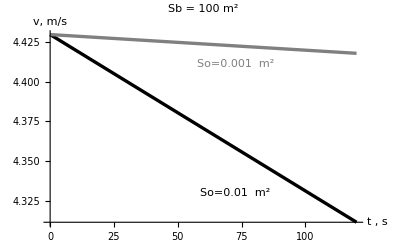

```mathematica
rys1=Plot[v2a[t]/.{So->0.01,Sb->100},{t,0,120},
PlotStyle->{Black,Thickness[0.006]}];
rys2=Plot[v2a[t]/.{So->0.001,Sb->100},{t,0,120},
PlotStyle->{Gray,Thickness[0.006]}];


Show[rys1,rys2,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm[" Sb = 100 m^2",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
AxesLabel->{"t , s","v,  m/s "},
Prolog->{Text[StyleForm["So=0.01  m^2",FontColor->Black],
Scaled[{0.60,0.17}]],
Text[StyleForm["So=0.001  m^2",FontColor->Gray],
Scaled[{0.60,0.83}]]}]
```

### Sporządzenie wykresu obrazującego zależność prędkości wypływu cieczy z otworu od czasu, dla pola powierzchni basenu S_b = 10 [m^2] i dwóch powierzchni otworu: S_o = 0.01 [m^2] i S_o = 0.001 [m^2].

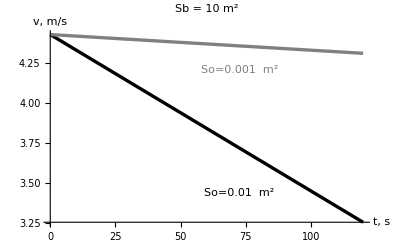

```mathematica
rys3=Plot[v2a[t]/.{So->0.01,Sb->10},{t,0,120},
PlotStyle->{Black,Thickness[0.006]}];
rys4=Plot[v2a[t]/.{So->0.001,Sb->10},{t,0,120},
PlotStyle->{Gray,Thickness[0.006]}];


Show[rys3,rys4,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm[" Sb = 10 m^2",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
AxesLabel->{"t, s","v,  m/s "},
Prolog->{Text[StyleForm["So=0.01  m^2",FontColor->Black],
Scaled[{0.60,0.17}]],
Text[StyleForm["So=0.001  m^2",FontColor->Gray],
Scaled[{0.60,0.80}]]}]
```

## Wykreślenie trajektorii strumienia wody wypływającej z otworu.

#### Obliczenie zależności wysokości strumienia wody wypływającej z otworu ( "y" ) od odległości od ściany basenu ( "x" ) i przypisanie tej wysokości nowej nazwy ( "y_1" ).

```mathematica
F=Solve[{x==v×t,y==h1-(g×t^2)/2},{y,t}]
y1=y/.F[[1,1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y→(0.005 (200. v^2-981. x^2))/v^2,t→x/v}}

(0.005 (200. v^2-981. x^2))/v^2

#### Wprowadzenie wartości dla pola powierzchni basenu ( "S_b" ) i otworu ( "S_o" ).

```mathematica
So=0.01;   (* m^2 *)
```

```mathematica
Sb=10;       (* m^2 *)
```

```mathematica
y2[t_]=y1/.{v->v2a[t]}
```

(0.0254842 (39.24 (100.-0.442945 t+0.0004905 t^2)-981. x^2))/(100.-0.442945 t+0.0004905 t^2)

#### Wyznaczenie zasięgu strumienia wody wypływającej z otworu ( "z[t]" ).

```mathematica
G=Solve[y2[t]==0,x]
z[t_]=x/.G[[2,1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-2.37809×10^-8 √(7.07297×10^15-3.13294×10^13 t+3.46929×10^10 t^2)},{x→2.37809×10^-8 √(7.07297×10^15-3.13294×10^13 t+3.46929×10^10 t^2)}}

2.37809×10^-8 √(7.07297×10^15-3.13294×10^13 t+3.46929×10^10 t^2)

#### Sporządzenie animacji obrazującej zmianę trajektorii strumienia wody wypływającej z otworu w czasie.

```mathematica
Trajektoria[t_] :=Plot[y2[t],{x,0,z[t]},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
(*PlotLabel->StyleForm[StringForm[" t =   `` s  ",t],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],*)
PlotStyle->{{Black,Thickness[0.006]}},
AxesLabel->{" x, m","y, m"},PlotRange->{{0,2},{0,1.2}}]
```

```mathematica
(*Do[Print[Trajektoria [t]],{t,0,300}]*)
```

```mathematica
manipulator=Manipulate[Trajektoria[t],{t,0,300},SaveDefinitions->True]
```